## Kerbin Ascent Stuff

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/kids/Documents/Physics 230

```mathematica
kerbinPressureDataRawPascals=Import["kerbin_altitude_vs_pressure.csv"];
```

```mathematica
kpdataPascals=Delete[kerbinPressureDataRawPascals,1];
```

```mathematica
kpequation[h_]=Interpolation[kpdataPascals,h];
```

```mathematica
kpequation[15006]
```

6.71429

### This equation does effectively nothing, but was supposed to predict ascent assuming no drag and constant gravity.

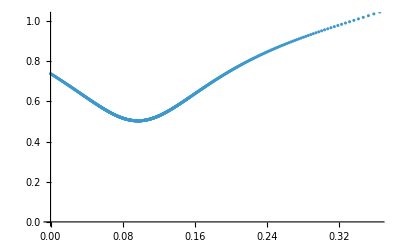

```mathematica
ascentProfileNoDrag[ti_,tf_,ψi_,vi_,xi_,yi_,n_Function,g_]:=Module[{ψ,Δψ,z0,ψ0,c,z,v,t,Δt,x,x0,Δx,y,y0,Δy,xytvψdata,xt,yt,xy,vt,ψt},
Δψ=ψi/100;ψ0=ψi;x0=xi;y0=yi;t=ti;xytvψdata={};
While[t<tf,
z0=-Tan[0.5ψ0];
c=-vi/(((-z0)^(n[t]-1))((1+(-z0))^2));
ψ=-(ψ0+Δψ);
z=-Tan[0.5(-ψ)];
v=(-c)*((-z)^(n[t]-1))*(1+((-z)^2));
Δt=((-c)/g)*((((-z)^(n[t]-1))*((1/(n[t]-1))+(((-z)^2)/(n[t]+1))))-(((-z0)^(n[t]-1))*((1/(n[t]-1))+(((-z0)^2)/(n[t]+1)))));
Δx=(0.5)*((vi*Sin[ψ0])+(v*Sin[(-ψ)]))*(Δt);
Δy=(0.5)*((vi*Sin[ψ0])+(v*Sin[(-ψ)]))*(Δt);
x=x0+Δx;y=y0+Δy;
x0=x;y0=y;ψ0=-ψ;
AppendTo[xytvψdata,{x,y,t,v,ψ0}];
t=t+Δt
];
xt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,x};
yt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,y};
xy=xytvψdata/.{x_,y_,t_,v_,ψ_}->{x,y};
vt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,v};
ψt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,ψ};
ListPlot[vt]
];
ascentProfileNoDrag[0,60,(Pi/8),1,0,68,(3E^(-5*#))&,9.81]
```

```mathematica
ascentProfileNoDrag[0,1000,15Degree,500,0,3000,(3E^(-5*#))&,32.174]
```

-Graphics-

### This is the equation that describes thrust of the Swivel rocket by altitude.

```mathematica
swivelThrustData={{0,167968.75},{79,168414},{83,168437},{103,168554},{164,168910},{337,169931},{492,170835},{868,173017},{1007,173818},{1548,176848},{2011,179354},{2532,182055},{3005,184393},{3618,187252},{4080,189281},{4669,191706},{5101,193374},{5549,195002},{6030,196646},{7039,199746},{8119,202581},{8914,204382},{9938,206344},{11115,208150},{11816,209039},{12906,210198},{13578,210796},{14047,211168},{14997,211825},{16106,212447},{17130,212912},{18581,213427},{20207,213849},{22173,214208},{23507,214386},{25801,214599},{27315,214695},{29155,214781},{31988,214866},{33787,214900},{36138,214932},{39336,214959},{39750,214962},{41479,214970},{43180,214977},{45647,214985},{48711,214991},{52243,214995},{55163,214997},{59254,214999},{63425,214999},{66987,215000},{68982,215000},{70000,}}
```

```mathematica
swivelThrust[h_]:=
```